```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
note={60,64,67};
timbro=Flatten[generateSetharesStandardHarmonicTimbre[midiToHertz[{#}],20]&/@note,1];
sigEquation=Total@Table[componente[[2]]*Sin[componente[[1]] 2Pi t],{componente,timbro}];
sound=AudioNormalize[AudioPad[Play[sigEquation,{t,0,1},SampleRate->44100],{0.01,0.01}]]
```

```mathematica
Export[
"audio-0.svg",
ListLinePlot[
AudioData[sound][[1]][[;;1000]],
ImageSize->1200,
Filling->Axis,
FillingStyle->{Directive[Opacity[0.01,Black],PointSize[0.001]]},
AspectRatio->1/3,
PlotRange->All,
PlotStyle->{Directive[Black,Thick,PointSize[0.0011]]},
InterpolationOrder->3,
PerformanceGoal->"Quality"
]]
```

audio-0.svg

```mathematica
Export[
"audio-1.png",
ListPlot[
AudioData[sound][[1]],
ImageSize->1200,
Filling->Axis,
FillingStyle->{Directive[Opacity[0.01,Black],PointSize[0.001]]},
AspectRatio->1/3,
PlotRange->All,
PlotStyle->{Directive[Black,Thick,PointSize[0.0011]]},
PerformanceGoal->"Quality"
]
]
```

audio-1.png

```mathematica
SetDirectory[NotebookDirectory[]];

fullSpectrum=False;



(*definisco la dimensione della mia stft*)
stftSize=4096;
(*definisco il mio hop size*)
hopsize=1024;

(*Importo il mio campione*)
audio=sound;

(*ricavo la frequenza di campionamento del campione*)
sr=QuantityMagnitude@AudioSampleRate[audio];

(*computo la STFT del segnale audio, con i parametri appena definiti*)
stft=ShortTimeFourier[audio,stftSize,hopsize,BlackmanWindow];

stftFreq=sr/stftSize;
```

```mathematica
data=Rescale@Map[ToPolarCoordinates[{Re[#],Im[#]}][[1]]/stftSize&,stft["Data"],{2}];

(*Export["sp.pdf",sp,OverwriteTarget->True]*)
```

```mathematica
Export[
"fourier.svg",
ListPlot[
Chop[data[[22]][[;;Round[stftSize/5]]],10^-2],
ImageSize->1200,
AspectRatio->1/2.5,
Filling->Axis,
FillingStyle->{Directive[Opacity[0.5,Black],PointSize[0.001]]},
PlotStyle->{Directive[Black,Thick,PointSize[0.0015]]},
PlotRange->All,
Ticks->{Table[{i,ToString[i*stftFreq//N]<>" Hz"},{i,1,stftSize,200}],Automatic},
PerformanceGoal->"Quality"
]
]
```

fourier.svg

```mathematica
man=Manipulate[
ListPlot[
Chop[data[[frame]][[;;Round[stftSize/5]]],10^-2],
ImageSize->1920,
AspectRatio->1/2.5,
Filling->Axis,
FillingStyle->{Directive[Opacity[0.5,Black],PointSize[0.001]]},
PlotStyle->{Directive[Black,Thick,PointSize[0.0015]]},
PlotRange->{Automatic,{0,1}},
Ticks->{Table[{i,ToString[i*stftFreq//N]<>" Hz"},{i,1,stftSize,200}],Automatic},
PerformanceGoal->"Quality"
],{frame,1,Length@data,1}]
```

```mathematica
Export["anim.mov",%,"ControlAppearance"->None];
```

```mathematica
Echo[sr=Floor[(44100. 2^0)+0.5],"sr: "];
Echo[stftSize=2^Ceiling[Log2[sr/16]],"stftSize: "];
Echo[halfStftSize=(stftSize/2)+1,"halfStftSize: "];
Echo[hopSize=stftSize/4,"hopSize: "];
Echo[stftSizePad=stftSize*8,"stftSizePad: "];
Echo[halfStftSizePad=(stftSizePad/2)+1,"halfStftSizePad: "];
Echo[freqFondFFT=sr/stftSizePad//N,"freqFondFFT: "];

Echo[armonicoFreqFondFFTDaApprossimare=Floor[(midiToHertz[{60.}]/freqFondFFT)+.5],"armonicoFreqFondFFTDaApprossimare: "];

QuietEcho@Echo[listFreqBin=(freqFondFFT*Range[0,stftSizePad-1])+0*(freqFondFFT/2.),"listFreqBin: "];
```

sr:   44100

stftSize:   4096

halfStftSize:   2049

hopSize:   1024

stftSizePad:   32768

halfStftSizePad:   16385

freqFondFFT:   1.34583

armonicoFreqFondFFTDaApprossimare:   194

```mathematica
ClearAll[audio,stft,magnitudine,harmonicsCouples,results,indici];

audio=Import["beethoven.mp3"];
audio=AudioSplit[audio,20][[1]];

stft=ShortTimeFourier[audio,stftSize,hopSize,BlackmanWindow,stftSizePad,FourierParameters->{-1, -1}];


magnitudine=Abs[stft["Data"]]^1;

binsCouples=FindPeaks[#,Log[100,stftSizePad]^2(*vedi manuale*)]&/@magnitudine[[All,;;halfStftSizePad]];

harmonicsCouples0={(#[[1]]-1)*freqFondFFT,#[[2]]}&/@#&/@binsCouples;
harmonicsCouples=Select[#,#[[2]]>=10^-20&&#[[1]]>=(2*freqFondFFT)&]&/@harmonicsCouples0;

results=Parallelize@Table[
(
indici =getUniquePairIndices[Length@harmonicsCouples[[i]]];
Total[dissonanceNumberCompilata/@Map[harmonicsCouples[[i,#]]&,indici]]
),
{i,Length@magnitudine}
];
```

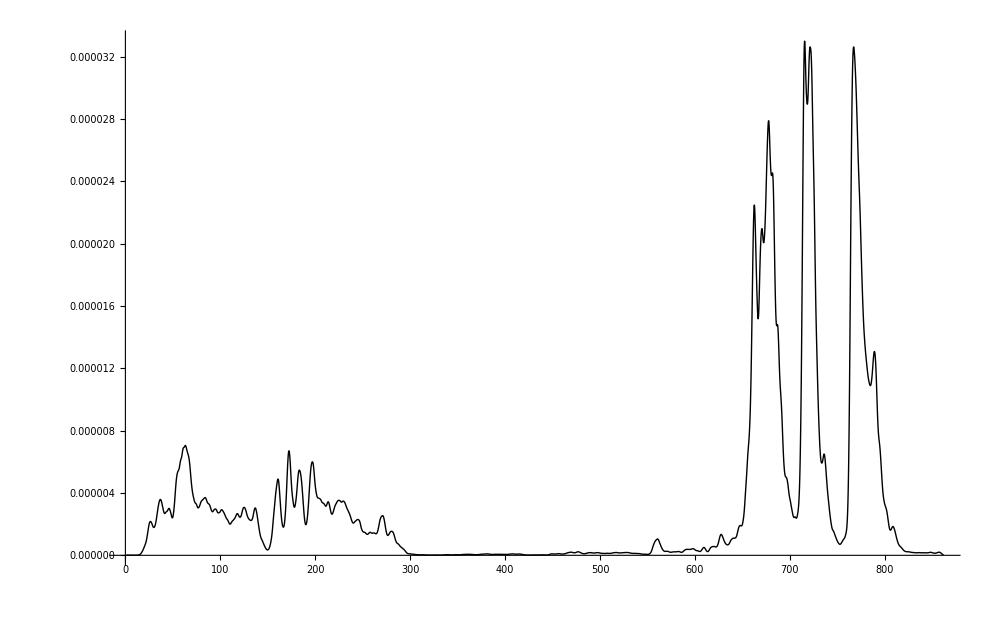

```mathematica
ListLinePlot[
GaussianFilter[results,3],
ImageSize->1000,
InterpolationOrder->10,
PlotStyle->{Directive[Black,Thick]},
PlotRange->All]
```

```mathematica
audio=Import["beethoven.mp3"];
```

```mathematica
AudioSplit[audio,20][[1]]
```

```mathematica
audio
```

```mathematica
int=Interpolation[results];

Table[
(
Export[NotebookDirectory[]<>"res/"<>ToString@N@(pos*30)<>".png",
Show[{
AudioPlot[AudioChannelSeparate[audio][[1]],ImageSize->1000,PerformanceGoal->"Quality",AspectRatio->1/2],
ListLinePlot[
N@Table[{Rescale[x,{1,Length@results},{0,AudioLength[audio][[1]]/44100}],30000*GaussianFilter[results,3][[x]]},{x,1,Length@results}],
PlotRange->All,
PlotStyle->{Directive[Red,Thick]}
],
Graphics[Line[{{pos,-1.5},{pos,1.5}}]]
}]
]
)
,{pos,0,AudioLength[audio][[1]]/44100,1/30}];
```

```mathematica
files=FileNames[NotebookDirectory[]<>"res/*.png"];

sortedFiles=SortBy[files,ToExpression@FileBaseName[#]&];

l=Import/@sortedFiles;
```

```mathematica
Export["bee.mov",{"Frames"->l,"Audio"->audio},(*{"Frames"->manFull,"Audio"->audio},*)"Duration"->(AudioLength[audio][[1]]/44100),"FrameRate"->30];
```